#### 5.-2

```mathematica
Solve[(m x e^2)/(4 π ϵ0 ℏ^2) == 1, x]
```

{{x→(4 π ϵ0 ℏ^2)/(e^2 m)}}

```mathematica
x0 = (4 π ϵ0 ℏ^2)/(e^2 m)
```

(4 π ϵ0 ℏ^2)/(e^2 m)

The energy scale is then

```mathematica
ℏ = Quantity[1, "ReducedPlanckConstant"]
m = IsotopeData["Hydrogen1", "AtomicMass"]
ϵ0 = Quantity[1, "ElectricConstant"]
e = Quantity[1, "ElementaryCharge"]
```

1 ℏ

1.00782503207 u

1 ε_0

1 e

```mathematica
Escale = (ℏ^2)/(2 m x0^2)
```

0.0031910632861 u e^4/(ε_0^2 ℏ^2)

```mathematica
UnitConvert[Quantity[0.00319106328605341949734961372871065429`11.52287874528034,("AtomicMassUnit" ("ElementaryCharge")^4)/(("ElectricConstant")^2 ("ReducedPlanckConstant")^2)],"eV"]
```

24995.7 eV

#### 5.-1

The matrix is of the form

```mathematica
{
{ (2/Δx^2)-(2/Δx), (-1/Δx^2), 0, 0, 0, 0, 0},
{(-1/Δx^2), (2/Δx^2)-(2/(2Δx)), (-1/Δx^2), 0, 0, 0, 0},
{0, (-1/Δx^2),(2/Δx^2)-(2/(3Δx)) , (-1/Δx^2), 0, 0, 0},
{0, 0,(-1/Δx^2) , (2/Δx^2)-(2/(4Δx)),  (-1/Δx^2), 0, 0},
{0,0,0, (-1/Δx^2),(2/Δx^2)-(2/(5Δx)), (-1/Δx^2),0},
{0,0,0,0, (-1/Δx^2),(2/Δx^2)-(2/(6Δx)), (-1/Δx^2)}
}
```

{{2/Δx^2-2/Δx,-1/Δx^2,0,0,0,0,0},{-1/Δx^2,2/Δx^2-1/Δx,-1/Δx^2,0,0,0,0},{0,-1/Δx^2,2/Δx^2-2/(3 Δx),-1/Δx^2,0,0,0},{0,0,-1/Δx^2,2/Δx^2-1/(2 Δx),-1/Δx^2,0,0},{0,0,0,-1/Δx^2,2/Δx^2-2/(5 Δx),-1/Δx^2,0},{0,0,0,0,-1/Δx^2,2/Δx^2-1/(3 Δx),-1/Δx^2}}

In general, the value of the main diagonal entry is (2/Δx^2)-(2/(NΔx)), and the value of the super- and sub-diagonal entries is (-1/Δx^2).

#### 5.0

```mathematica
ψ[j_] := A Exp[ⅈ π n j Δx]
En = Solve[-(ψ[j+1] - 2ψ[j] + ψ[j-1])/(Δx^2) == Ent ψ[j], Ent][[1]][[1]]
```

Ent→(ⅇ^(-ⅈ j n π Δx) (-ⅇ^(ⅈ (-1+j) n π Δx)+2 ⅇ^(ⅈ j n π Δx)-ⅇ^(ⅈ (1+j) n π Δx)))/Δx^2

```mathematica
Limit[(ⅇ^(-ⅈ j n π Δx) (-ⅇ^(ⅈ (-1+j) n π Δx)+2 ⅇ^(ⅈ j n π Δx)-ⅇ^(ⅈ (1+j) n π Δx)))/Δx^2, Δx -> 0]
```

n^2 π^2

#### 5.1

```mathematica
Pbox[xf_, N_] := Module[{Δx, H, j},
Δx = xf/(N+1);
H = Table[Table[0, {x, 1, N}], {x, 1, N}];
H[[1]][[1]] = 2/(Δx^2);
H[[1]][[2]] = -1/(Δx^2);
For[j=2, j<N, j++,
H[[j]][[j-1]] = -1/(Δx^2);
H[[j]][[j]] = 2/(Δx^2);
H[[j]][[j+1]] = -1/(Δx^2);
];
H[[N]][[N-1]] = -1/(Δx^2);
H[[N]][[N]] = 2/(Δx^2);
Return[H];
]
```

```mathematica
B = Pbox[1,100];
```

```mathematica
Evals = Eigenvalues[B];
```

```mathematica
EvalsSorted = Sort[Evals, Less];
```

```mathematica
a=N[EvalsSorted[[1]]]
```

9.86881

```mathematica
b=N[EvalsSorted[[2]]]
```

39.4657

```mathematica
b-a
```

29.5969

```mathematica
3 π^2
```

3 π^2

```mathematica
N[%]
```

29.6088

The difference between the two smallest eigenvalues is about 3π^2, as predicted in 5.0.

#### 5.2

```mathematica
Pbox2[xf_, N_] := Module[{Δx, H, j},
Δx = xf/(N+1);
H = Table[Table[0, {x, 1, N}], {x, 1, N}];
H[[1]][[1]] = 2/(Δx^2) - (2/Δx);
H[[1]][[2]] = -1/(Δx^2);
For[j=2, j<N, j++,
H[[j]][[j-1]] = -1/(Δx^2);
H[[j]][[j]] = 2/(Δx^2) - (2/(j Δx));
H[[j]][[j+1]] = -1/(Δx^2);
];
H[[N]][[N-1]] = -1/(Δx^2);
H[[N]][[N]] = 2/(Δx^2) - (2/(N Δx));
Return[H];
]
```

```mathematica
H2 = N[Pbox2[30,10000]];
```

```mathematica
evals = Sort[Eigenvalues[H2], Less]
```

{-0.999998,-0.25,-0.110847,-0.0492784,0.0266294,0.129871,0.258548,9986,444533.,444533.,444533.,444533.,444533.,444533.,444533.}
 |  |  |  |

```mathematica
evalsSelect= evals[[1;;4]]
```

{-0.999998,-0.25,-0.110847,-0.0492784}

```mathematica
scaledEnergies = evalsSelect * Escale
```

{-0.00319106 u e^4/(ε_0^2 ℏ^2),-0.000797765 u e^4/(ε_0^2 ℏ^2),-0.000353721 u e^4/(ε_0^2 ℏ^2),-0.00015725 u e^4/(ε_0^2 ℏ^2)}

```mathematica
eVEs = UnitConvert[scaledEnergies, "Electronvolts"]
```

{-24995.7 eV,-6248.93 eV,-2770.71 eV,-1231.75 eV}

These values should scale with 1/n^2, since the

```mathematica
vals = Table[{n, eVEs[[n]]}, {n, 1, 4}]
```

{{1,-24995.7 eV},{2,-6248.93 eV},{3,-2770.71 eV},{4,-1231.75 eV}}

```mathematica
NonlinearModelFit[vals, A/ n^2, {A}, n]
```

FittedModel[(-24975.9 eV)/n^2]

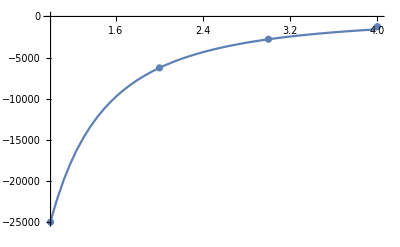

```mathematica
Show[Plot[FittedModel[Quantity[-24975.855442853346, "Electronvolts"]/n^2][n], {n, 1, 4}], 
ListPlot[vals]]
```

This fit seems to work well.